## Monoprotic Acid (inverse solution method) A and A+(HA) refer to deprotaned and protanated acid

#### In the case of lysine head group, NH2 and NH3+ (A and HA)

### System of Reactions (1) [H+]+[Na+]+[A+]=[OH-] (charge conservation) (2) Ca = [A+] + [A] (mass conservation) (3a) NH3+ + OH- <=> NH2 + H2O (ka) A*H/HA==Ka (3b)H+ + NH2 <=> NH3+ (ka’) (4) H2O <=> H+ + OH- (kw) (5/6) Volume of bases and acids

(2 L^2 (h+R))/(h+2 R)

```mathematica
Clear["`*"]
Reduce[{Eliminate[{(H*A/(HA))==Ka,
H*OH==Kw,
CA==HA+A,
H+B+HA==OH+X,
X==A+HA,
B==Vb*Binit/(Va+Vb),
CA==Va*Ainit/(Va+Vb)},{HA,A,OH,B,CA,X},InverseFunctions->True],Vb>0}]
```

(((Vb>0&&Va==0&&Kw==0)||(((Re[Kw]<0&&Vb>0)||(Re[Kw]==0&&((Im[Kw]<0&&Vb>0)||(Im[Kw]>0&&Vb>0)))||(Re[Kw]>0&&Vb>0))&&Va==0&&Ka==0))&&H==0)||(((Re[H]<0&&Vb>0)||(Re[H]==0&&((Im[H]<0&&Vb>0)||(Im[H]>0&&Vb>0)))||(Re[H]>0&&Vb>0))&&Va==0&&Ka==-H)||(((Re[Va]<0&&(0<Vb<-Re[Va]||(Vb==-Re[Va]&&(Im[Va]<0||Im[Va]>0))||Vb>-Re[Va]))||(Re[Va]==0&&Vb>0&&(Im[Va]<0||Im[Va]>0))||(Re[Va]>0&&Vb>0))&&H==0&&Ka==0)||(((Re[Va]<0&&((Im[Va]<0&&((Re[Ka]<0&&Vb>0)||(Re[Ka]==0&&((Im[Ka]<0&&Vb>0)||(Im[Ka]>0&&Vb>0)))||(Re[Ka]>0&&Vb>0)))||(Im[Va]==0&&((Re[Ka]<0&&(0<Vb<-Re[Va]||Vb>-Re[Va]))||(Re[Ka]==0&&((Im[Ka]<0&&(0<Vb<-Re[Va]||Vb>-Re[Va]))||(Im[Ka]>0&&(0<Vb<-Re[Va]||Vb>-Re[Va]))))||(Re[Ka]>0&&(0<Vb<-Re[Va]||Vb>-Re[Va]))))||(Im[Va]>0&&((Re[Ka]<0&&Vb>0)||(Re[Ka]==0&&((Im[Ka]<0&&Vb>0)||(Im[Ka]>0&&Vb>0)))||(Re[Ka]>0&&Vb>0)))))||(Re[Va]==0&&((Im[Va]<0&&((Re[Ka]<0&&Vb>0)||(Re[Ka]==0&&((Im[Ka]<0&&Vb>0)||(Im[Ka]>0&&Vb>0)))||(Re[Ka]>0&&Vb>0)))||(Im[Va]>0&&((Re[Ka]<0&&Vb>0)||(Re[Ka]==0&&((Im[Ka]<0&&Vb>0)||(Im[Ka]>0&&Vb>0)))||(Re[Ka]>0&&Vb>0)))))||(Re[Va]>0&&((Re[Ka]<0&&Vb>0)||(Re[Ka]==0&&((Im[Ka]<0&&Vb>0)||(Im[Ka]>0&&Vb>0)))||(Re[Ka]>0&&Vb>0))))&&Kw==0&&H==0)||(((((Re[H]<0&&((Im[H]<0&&((Re[Ka]<-Re[H]&&Vb>0)||(Re[Ka]==-Re[H]&&((Im[Ka]<(-Im[H]^2+Re[H]^2+Re[H] Re[Ka])/Im[H]&&Vb>0)||(Im[Ka]>(-Im[H]^2+Re[H]^2+Re[H] Re[Ka])/Im[H]&&Vb>0)))||(Re[Ka]>-Re[H]&&Vb>0)))||(Im[H]==0&&((Re[Ka]<-Re[H]&&Vb>0)||(Re[Ka]==-Re[H]&&((Im[Ka]<0&&Vb>0)||(Im[Ka]>0&&Vb>0)))||(Re[Ka]>-Re[H]&&Vb>0)))||(Im[H]>0&&((Re[Ka]<-Re[H]&&Vb>0)||(Re[Ka]==-Re[H]&&((Im[Ka]<(-Im[H]^2+Re[H]^2+Re[H] Re[Ka])/Im[H]&&Vb>0)||(Im[Ka]>(-Im[H]^2+Re[H]^2+Re[H] Re[Ka])/Im[H]&&Vb>0)))||(Re[Ka]>-Re[H]&&Vb>0)))))||(Re[H]==0&&((Im[H]<0&&((Re[Ka]<0&&Vb>0)||(Re[Ka]==0&&((Im[Ka]<-Im[H]&&Vb>0)||(Im[Ka]>-Im[H]&&Vb>0)))||(Re[Ka]>0&&Vb>0)))||(Im[H]>0&&((Re[Ka]<0&&Vb>0)||(Re[Ka]==0&&((Im[Ka]<-Im[H]&&Vb>0)||(Im[Ka]>-Im[H]&&Vb>0)))||(Re[Ka]>0&&Vb>0)))))||(Re[H]>0&&((Im[H]<0&&((Re[Ka]<-Re[H]&&Vb>0)||(Re[Ka]==-Re[H]&&((Im[Ka]<(-Im[H]^2+Re[H]^2+Re[H] Re[Ka])/Im[H]&&Vb>0)||(Im[Ka]>(-Im[H]^2+Re[H]^2+Re[H] Re[Ka])/Im[H]&&Vb>0)))||(Re[Ka]>-Re[H]&&Vb>0)))||(Im[H]==0&&((Re[Ka]<-Re[H]&&Vb>0)||(Re[Ka]==-Re[H]&&((Im[Ka]<0&&Vb>0)||(Im[Ka]>0&&Vb>0)))||(Re[Ka]>-Re[H]&&Vb>0)))||(Im[H]>0&&((Re[Ka]<-Re[H]&&Vb>0)||(Re[Ka]==-Re[H]&&((Im[Ka]<(-Im[H]^2+Re[H]^2+Re[H] Re[Ka])/Im[H]&&Vb>0)||(Im[Ka]>(-Im[H]^2+Re[H]^2+Re[H] Re[Ka])/Im[H]&&Vb>0)))||(Re[Ka]>-Re[H]&&Vb>0))))))&&Va==0)||(((Re[H]<0&&((Re[Va]<0&&(0<Vb<-Re[Va]||(Vb==-Re[Va]&&(Im[Va]<0||Im[Va]>0))||Vb>-Re[Va]))||(Re[Va]==0&&Vb>0&&(Im[Va]<0||Im[Va]>0))||(Re[Va]>0&&Vb>0)))||(Re[H]==0&&((Im[H]<0&&((Re[Va]<0&&(0<Vb<-Re[Va]||(Vb==-Re[Va]&&(Im[Va]<0||Im[Va]>0))||Vb>-Re[Va]))||(Re[Va]==0&&Vb>0&&(Im[Va]<0||Im[Va]>0))||(Re[Va]>0&&Vb>0)))||(Im[H]>0&&((Re[Va]<0&&(0<Vb<-Re[Va]||(Vb==-Re[Va]&&(Im[Va]<0||Im[Va]>0))||Vb>-Re[Va]))||(Re[Va]==0&&Vb>0&&(Im[Va]<0||Im[Va]>0))||(Re[Va]>0&&Vb>0)))))||(Re[H]>0&&((Re[Va]<0&&(0<Vb<-Re[Va]||(Vb==-Re[Va]&&(Im[Va]<0||Im[Va]>0))||Vb>-Re[Va]))||(Re[Va]==0&&Vb>0&&(Im[Va]<0||Im[Va]>0))||(Re[Va]>0&&Vb>0))))&&Ka==0))&&Binit==(-H^3 Va-H^2 Ka Va+H Kw Va+Ka Kw Va-H^3 Vb-H^2 Ka Vb+H Kw Vb+Ka Kw Vb)/(H^2 Vb+H Ka Vb))||(((Im[Ka]<0&&((Re[Va]<0&&((Im[Va]<0&&Vb>0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))||(Im[Va]==0&&((0<Vb<-Re[Va]&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))||(Vb>-Re[Va]&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))))||(Im[Va]>0&&Vb>0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))))||(Re[Va]==0&&((Im[Va]<0&&Vb>0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))||(Im[Va]>0&&Vb>0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))))||(Re[Va]>0&&Vb>0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))))||(Im[Ka]==0&&((Re[Va]<0&&((Im[Va]<0&&Vb>0&&((Re[Ka]<0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))||(Re[Ka]>0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))))||(Im[Va]==0&&((0<Vb<-Re[Va]&&((Re[Ka]<0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))||(Re[Ka]>0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))))||(Vb>-Re[Va]&&((Re[Ka]<0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))||(Re[Ka]>0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))))))||(Im[Va]>0&&Vb>0&&((Re[Ka]<0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))||(Re[Ka]>0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))))))||(Re[Va]==0&&((Im[Va]<0&&Vb>0&&((Re[Ka]<0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))||(Re[Ka]>0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))))||(Im[Va]>0&&Vb>0&&((Re[Ka]<0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))||(Re[Ka]>0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))))))||(Re[Va]>0&&Vb>0&&((Re[Ka]<0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))||(Re[Ka]>0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))))))||(Im[Ka]>0&&((Re[Va]<0&&((Im[Va]<0&&Vb>0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))||(Im[Va]==0&&((0<Vb<-Re[Va]&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))||(Vb>-Re[Va]&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))))||(Im[Va]>0&&Vb>0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))))||(Re[Va]==0&&((Im[Va]<0&&Vb>0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))||(Im[Va]>0&&Vb>0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0))))||(Re[Va]>0&&Vb>0&&(Im[H]<0||(Im[H]==0&&(Re[H]<0||Re[H]>0))||Im[H]>0)))))&&Ainit==(H^3 Va+H^2 Ka Va-H Kw Va-Ka Kw Va+Binit H^2 Vb+H^3 Vb+Binit H Ka Vb+H^2 Ka Vb-H Kw Vb-Ka Kw Vb)/(H Ka Va))

```mathematica
FullSimplify[Solve[Ainit==(H^3 Va+H^2 Ka Va-H Kw Va-Ka Kw Va+Binit H^2 Vb+H^3 Vb+Binit H Ka Vb+H^2 Ka Vb-H Kw Vb-Ka Kw Vb)/(H Ka Va),Vb]]
```

{{Vb→((H (Ainit Ka-H (H+Ka))+(H+Ka) Kw) Va)/((H+Ka) (H (Binit+H)-Kw))}}

```mathematica
Clear["`*"]
Reduce[Eliminate[{(H^n*A/(HA))==Ka^n,
H*OH==Kw,
CA==HA+A,
H+B+HA==OH+X,
X==A+HA,
B==Vb*Binit/(Va+Vb),
CA==Va*Ainit/(Va+Vb)},{HA,A,OH,B,CA,X},InverseFunctions->True]]
```

(Ka==0&&Re[n]>0&&H==0&&Va+Vb≠0)||(Kw==0&&H==0&&Va+Vb≠0)||(H==0&&Ka==0&&Re[n]>0&&Va+Vb≠0)||(Ka==0&&Re[n]>0&&((H Vb≠0&&Binit==-((H^2-Kw) (Va+Vb))/(H Vb)&&Va+Vb≠0)||(Vb≠0&&Kw==0&&H==0&&Va+Vb≠0)||(Vb==0&&Va≠0&&(H==-√Kw||H==√Kw))))||(Va==0&&Vb≠0&&((C[1]∈ℤ&&H≠0&&Ka≠0&&Log[H]-Log[Ka]≠0&&n==-(ⅈ π+2 ⅈ π C[1])/(Log[H]-Log[Ka]))||(H==0&&Ka==0&&Re[n]>0)))||(Va==0&&H≠0&&Binit==(-H^2+Kw)/H&&Vb≠0)||(Va==0&&Kw==0&&H==0&&Vb≠0)||(H Ka^n Va (Va+Vb)≠0&&Ainit==-(Ka^-n (-H^(2+n) Va-H^2 Ka^n Va+H^n Kw Va+Ka^n Kw Va-Binit H^(1+n) Vb-H^(2+n) Vb-Binit H Ka^n Vb-H^2 Ka^n Vb+H^n Kw Vb+Ka^n Kw Vb))/(H Va))

```mathematica
FullSimplify[Solve[%267,Vb]]
```

$Aborted

```mathematica
Solve[Ainit==-(Ka^-n (-H^(2+n) Va-H^2 Ka^n Va+H^n Kw Va+Ka^n Kw Va-Binit H^(1+n) Vb-H^(2+n) Vb-Binit H Ka^n Vb-H^2 Ka^n Vb+H^n Kw Vb+Ka^n Kw Vb))/(H Va),Vb]
```

{{Vb→-((H^(2+n)-Ainit H Ka^n+H^2 Ka^n-H^n Kw-Ka^n Kw) Va)/((H^n+Ka^n) (Binit H+H^2-Kw))}}

### The solution for Vb needs to be offset by the equivalence point volume Ainit*Va/Binit (not sure where this issue comes from yet.

```mathematica
Clear["`*"]
pH=List[4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12]
Hlist=Table[10^(-pH[[i]]),{i,Length[pH]}]
```

{4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12}

{0.0000316228,1/100000,3.16228×10^-6,1/1000000,3.16228×10^-7,1/10000000,3.16228×10^-8,1/100000000,3.16228×10^-9,1/1000000000,3.16228×10^-10,1/10000000000,3.16228×10^-11,1/100000000000,3.16228×10^-12,1/1000000000000}

```mathematica
Va=2.5
Ainit=0.004
Binit=0.1
Ka=10^(-8)
Kw=10^(-14)
Vb[H_]:=(-H^2 (Ainit+H+Ka) Va+(H+Ka) Kw Va)/((H+Ka) (H (Binit+H)-Kw))+Ainit*Va/Binit
VbCorrect[H_]:=(-Va*(H^3+Ka*H^2-(Kw+Ka*Ainit)*H-Kw*Ka))/(H^2 Ka+Binit H (H+Ka)-(H+Ka) Kw)
```

2.5

0.004

0.1

1/100000000

1/100000000000000

```mathematica
0.1
```

0.1

```mathematica
Thread[{Table[Vb[Hlist[[i]]],{i,Length[Hlist]}],pH}]
```

{{-0.000727096,4.5},{-0.000140062,5},{0.000239405,5.5},{0.000966329,6},{0.0030585,6.5},{0.00909091,7},{0.0240322,7.5},{0.0500243,8},{0.0760529,8.5},{0.0911582,9},{0.0977245,9.5},{0.101511,10},{0.107615,10.5},{0.125152,11},{0.181606,11.5},{0.377767,12}}

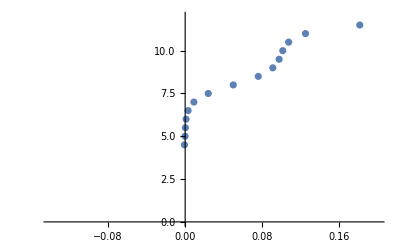

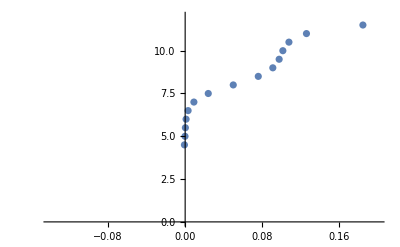

```mathematica
ListPlot[Thread[{Table[Vb[Hlist[[i]]],{i,Length[Hlist]}],pH}],PlotRange->{{-0.14,0.2},Automatic}]
ListPlot[Thread[{Table[VbCorrect[Hlist[[i]]],{i,Length[Hlist]}],pH}],PlotRange->{{-0.14,0.2},Automatic}]
```

```mathematica
Clear["`*"]
pH=List[4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12]
Hlist=Table[10^(-pH[[i]]),{i,Length[pH]}]
```

{4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12}

{0.0000316228,1/100000,3.16228×10^-6,1/1000000,3.16228×10^-7,1/10000000,3.16228×10^-8,1/100000000,3.16228×10^-9,1/1000000000,3.16228×10^-10,1/10000000000,3.16228×10^-11,1/100000000000,3.16228×10^-12,1/1000000000000}

```mathematica
Vb16={0,1,2,4,6,8,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220}
pH16={4.34,4.7,4.83,5.04,5.25,5.4,5.5,5.83,6.13,6.46,6.69,6.83,6.95,7.05,7.14,7.23,7.3,7.36,7.43,7.52,7.61,7.8,7.99,8.15,8.3,8.5,8.74,9.17,9.66,10.24,10.66,10.89,11.06,11.2,11.3}
```

{0,1,2,4,6,8,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220}

{4.34,4.7,4.83,5.04,5.25,5.4,5.5,5.83,6.13,6.46,6.69,6.83,6.95,7.05,7.14,7.23,7.3,7.36,7.43,7.52,7.61,7.8,7.99,8.15,8.3,8.5,8.74,9.17,9.66,10.24,10.66,10.89,11.06,11.2,11.3}

```mathematica
Va=5
Ainit=0.004
Binit=0.1
Ka=10^(-8)
Kw=10^(-14)
Vb[H_]:=((H (Ainit Ka-H (H+Ka))+(H+Ka) Kw) Va)/((H+Ka) (H (Binit+H)-Kw))
```

5

0.004

0.1

1/100000000

1/100000000000000

```mathematica
γ=0.1
Vbγ[H_]:=-(Va (Ainit H^2+(H^2-Kw) (H+Ka γ)))/((H (Binit+H)-Kw) (H+Ka γ))+Ainit*Va/Binit
```

0.1

```mathematica
q=2.5
Vbq[H_]:=-(((H+Ka) (H^2-Kw)+Ainit H^2 q) Va)/((H+Ka) (H (Binit+H)-Kw))+q*Ainit*Va/Binit
```

2.5

```mathematica
Vbq2[H_]:=-((Ainit H+H^2+H^2 (Ka/H)^(1/q)-Kw-(Ka/H)^(1/q) Kw) Va)/((1+(Ka/H)^(1/q)) (Binit H+H^2-Kw))+(Ainit*Va/Binit)
Vbq3[H_]:=-((H^2-Ainit H (Ka/H)^(1/q)+H^2 (Ka/H)^(1/q)-Kw-(Ka/H)^(1/q) Kw) Va)/((1+(Ka/H)^(1/q)) (Binit H+H^2-Kw))
n=0.6
Vbn[H_]:=-((H^(2+n)-Ainit H Ka^n+H^2 Ka^n-H^n Kw-Ka^n Kw) Va)/((H^n+Ka^n) (Binit H+H^2-Kw))
```

0.6

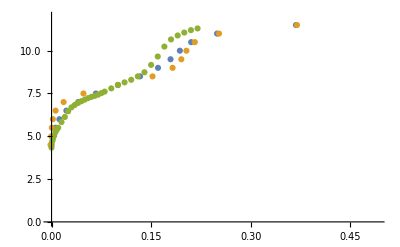

```mathematica
ListPlot[{Thread[{Table[Vbn[Hlist[[i]]],{i,Length[Hlist]}],pH}],Thread[{Table[Vb[Hlist[[i]]],{i,Length[Hlist]}],pH}],Thread[{Table[Vb16[[i]]/1000,{i,Length[Vb16]}],pH16}]},PlotRange->{Automatic,Automatic}]
```

```mathematica
Thread[{Table[1/((Log10[Vbq[Hlist[[i]]]*Binit/(Va+Vbq[Hlist[[i]]])]+Log10[q])/(Log10[Vbq[Hlist[[i]]]*Binit/(Va+Vbq[Hlist[[i]]])])),{i,Length[Hlist]}],pH}]
```

{{1.08572+0.0278531 ⅈ,4.5},{1.07098,5},{1.09601,5.5},{1.11021,6},{1.12766,6.5},{1.15031,7},{1.17832,7.5},{1.20681,8},{1.227,8.5},{1.23676,9},{1.24052,9.5},{1.24214,10},{1.24378,10.5},{1.24778,11},{1.25949,11.5},{1.29244,12}}

0.8

0.9

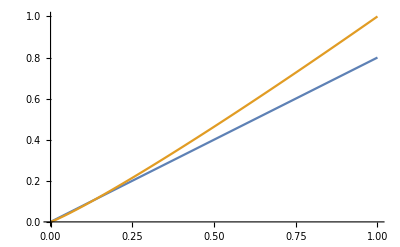

```mathematica
f1[B_,n_]:=B*n
f2[B_,x_]:=B^(1/x)
val1=0.8
val2=0.9
Plot[{f1[b,val1],f2[b,val2]},{b,0,1.0}]
```

```mathematica
pH0=pH16[[1]]
H0=10^(-pH0)
OH0=10^(-14+pH0)
pKa0=7.98
Ka0=10^(-pKa0)
m=0.6
```

4.34

0.0000457088

2.18776×10^-10

7.98

1.04713×10^-8

0.6

```mathematica
NSolve[{H0+HA==OH0+X,X==A+HA,H0^m*A/HA==Ka0^m}]
```

{{A→0.0000457086,HA→0.00698229,X→0.007028}}

```mathematica
NSolve[{H0+HA==OH0,H0^m*A/HA==Ka0^m}]
```

```mathematica
0.00039807405744134915/0.000010963869950592495
```

36.3078

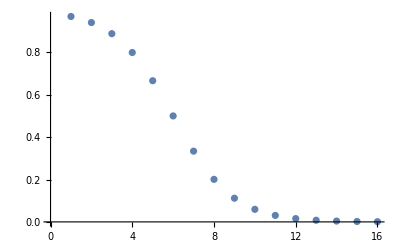

```mathematica
theta[H_,Ka_,n_]:=H^n/(Ka^n+H^n)
ListPlot[Thread[Table[theta[Hlist[[i]],Ka0,m],{i,Length[Hlist]}],Table[Hlist[[i]],{i,Length[Hlist]}]],PlotRange->{Automatic,Automatic}]
```

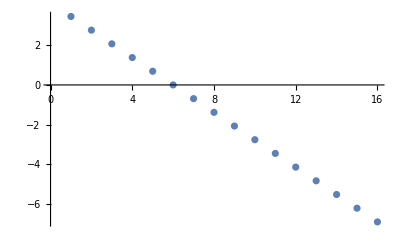

```mathematica
ListPlot[Thread[Table[Log[theta[Hlist[[i]],Ka0,m]/(1-theta[Hlist[[i]],Ka0,m])],{i,Length[Hlist]}],Table[Log[Hlist[[i]]],{i,Length[Hlist]}]]]
```

```mathematica
Table[theta[Hlist[[i]],Ka0,m],{i,Length[Hlist]}]
```

{}

### System of Reactions (with counter ion X) (products / reactants) (1) [H+] + [Na+] + [A+] = [OH-] + [X-] (charge conservation) (2) Ca = [A+] + [A] + [AX] (mass conservation) (3a) NH3+ + OH- <=> NH2 + H2O (ka’) (3b)H+ + NH2 <=> NH3+ (ka) (4) H2O <=> H+ + OH- (kw) (5/6) Volume of bases and acid (7) [X-] = [A+] + [A] (8) [A+] + [X-] == [AX] (ks)

```mathematica
Clear["`*"]
```

```mathematica
Eliminate[{(H^n*A/(HA))==Ka^n,
H*OH==Kw,
(HA*X)/(AX)==Ks,
CA==HA+A+AX,
H+B+HA==OH+X,
X==A+HA,
B==Vb*Binit/(Va+Vb),
CA==(Va*Ainit)/(Va+Vb)},{OH,HA,B,CA,AX,A,X}]
```

H^n (H^n+Ka^n) Kw^2+H Kw (-2 H^(1+2 n)-2 H^(1+n) Ka^n-H^n Ka^n Ks-Ka^(2 n) Ks-(2 Binit H^(2 n) Vb)/(Va+Vb)-(2 Binit H^n Ka^n Vb)/(Va+Vb))==H^2 (-H^(2+2 n)-H^(2+n) Ka^n-H^(1+n) Ka^n Ks+Ainit Ka^(2 n) Ks-H Ka^(2 n) Ks-(Binit^2 H^(2 n) Vb^2)/(Va+Vb)^2-(Binit^2 H^n Ka^n Vb^2)/(Va+Vb)^2-(2 Binit H^(1+2 n) Vb)/(Va+Vb)-(2 Binit H^(1+n) Ka^n Vb)/(Va+Vb)-(Binit H^n Ka^n Ks Vb)/(Va+Vb)-(Ainit Ka^(2 n) Ks Vb)/(Va+Vb)-(Binit Ka^(2 n) Ks Vb)/(Va+Vb))&&Va+Vb≠0

```mathematica
FullSimplify[Solve[%54,Vb]]
```

{{Vb→((-H^(3/2) Ka^n √Ks √(Ainit^2 H Ka^(2 n) Ks+Binit^2 H (H^n+Ka^n)^2 Ks+2 Ainit Binit (H^n+Ka^n) (H Ka^n Ks+2 H^n (H (Binit+H)-Kw)))-2 H^(2 n) (H^2-Kw) (H (Binit+H)-Kw)+H Ka^(2 n) Ks (Ainit H-H (Binit+2 H)+2 Kw)-H^n Ka^n (H^2 (2 H (H+Ks)+Binit (2 H+Ks))-2 H (Binit+2 H+Ks) Kw+2 Kw^2)) Va)/(2 (H^n+Ka^n) (H Ka^n Ks+H^n (H (Binit+H)-Kw)) (H (Binit+H)-Kw))},{Vb→((H^(3/2) Ka^n √Ks √(Ainit^2 H Ka^(2 n) Ks+Binit^2 H (H^n+Ka^n)^2 Ks+2 Ainit Binit (H^n+Ka^n) (H Ka^n Ks+2 H^n (H (Binit+H)-Kw)))-2 H^(2 n) (H^2-Kw) (H (Binit+H)-Kw)+H Ka^(2 n) Ks (Ainit H-H (Binit+2 H)+2 Kw)-H^n Ka^n (H^2 (2 H (H+Ks)+Binit (2 H+Ks))-2 H (Binit+2 H+Ks) Kw+2 Kw^2)) Va)/(2 (H^n+Ka^n) (H Ka^n Ks+H^n (H (Binit+H)-Kw)) (H (Binit+H)-Kw))}}

2.5

0.004

0.1

1/100000000

1/10

1/100000000000000

```mathematica
Clear["`*"]
Va=5
Ainit=0.004
Binit=0.1
Ka=10^(-6)
Ks=10^(4)
Kw=10^(-14)
Vb[H_]:=((-2 H^5-2 H^4 (Binit+Ka)+H Ka √Ks √(Ainit^2 Ka^2 Ks+Binit^2 (H+Ka)^2 Ks+2 Ainit Binit (H+Ka) (2 H (Binit+H)+Ka Ks-2 Kw))-H^2 (Binit+2 Ka) (Ka Ks-2 Kw)-2 H^3 (Ka (Binit+Ks)-2 Kw)+2 Ka (Ka Ks-Kw) Kw+H ((Ainit-Binit) Ka^2 Ks+2 Ka (Binit+Ks) Kw-2 Kw^2)) Va)/(2 (H+Ka) (H (Binit+H)-Kw) (H (Binit+H)+Ka Ks-Kw))
```

5

0.004

0.1

1/1000000

10000

1/100000000000000

#### Vb2, Charge conservation f: H + B + f*HA == OH + f*X Vb3, Mass conservation f: CA == (1 - f)*HA + A + f*AX Vb4, Ks reaction: (HA*X)/(f*AX)==Ks Vb5, Eliminating Ainit by adding (f)^2*Ainit/(1-f) ==Ks,

```mathematica
Vb2[H_,f_,Ks_]:=((-2 H^5-2 H^4 (Binit+Ka)+f H Ka √Ks √(Ainit^2 f^2 Ka^2 Ks+Binit^2 (H+Ka)^2 Ks+2 Ainit Binit (H+Ka) (2 H (Binit+H)+f Ka Ks-2 Kw))-H^2 (Binit+2 Ka) (f Ka Ks-2 Kw)-2 H^3 (Binit Ka+f Ka Ks-2 Kw)+2 Ka (f Ka Ks-Kw) Kw+H (f (-Binit+Ainit f) Ka^2 Ks+2 Ka (Binit+f Ks) Kw-2 Kw^2)) Va)/(2 (H+Ka) (H (Binit+H)-Kw) (H (Binit+H)+f Ka Ks-Kw))
Vb3[H_,f_,Ks_]:=((-2 f H (H^2-Kw) (H (Binit+H)-Kw)+Ka^2 Ks (Ainit H-H (Binit+2 H)+2 Kw)+Ka (H^2 (-2 f H (Binit+H)+(-1+f) (Binit+2 H) Ks)+2 H (f (Binit+2 H-Ks)+Ks) Kw-2 f Kw^2)+H Ka √Ks √(Ainit^2 Ka^2 Ks+Binit^2 (H-f H+Ka)^2 Ks+2 Ainit Binit (2 Binit f H (H+Ka)+Ka (H+Ka) Ks+f H (2 H (H+Ka)-Ka Ks)-2 f (H+Ka) Kw))) Va)/(2 (H (Binit+H)-Kw) (Binit f H (H+Ka)+Ka (H+Ka) Ks+f H (H (H+Ka)-Ka Ks)-f (H+Ka) Kw))
```

```mathematica
pH=List[4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12]
Hlist=Table[10^(-pH[[i]]),{i,Length[pH]}]
```

{4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12}

{0.0000316228,1/100000,3.16228×10^-6,1/1000000,3.16228×10^-7,1/10000000,3.16228×10^-8,1/100000000,3.16228×10^-9,1/1000000000,3.16228×10^-10,1/10000000000,3.16228×10^-11,1/100000000000,3.16228×10^-12,1/1000000000000}

{0,1,2,4,6,8,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220}

{4.34,4.7,4.83,5.04,5.25,5.4,5.5,5.83,6.13,6.46,6.69,6.83,6.95,7.05,7.14,7.23,7.3,7.36,7.43,7.52,7.61,7.8,7.99,8.15,8.3,8.5,8.74,9.17,9.66,10.24,10.66,10.89,11.06,11.2,11.3}

{{Vb[0.0000316228],4.5},{Vb[1/100000],5},{Vb[3.16228×10^-6],5.5},{Vb[1/1000000],6},{Vb[3.16228×10^-7],6.5},{Vb[1/10000000],7},{Vb[3.16228×10^-8],7.5},{Vb[1/100000000],8},{Vb[3.16228×10^-9],8.5},{Vb[1/1000000000],9},{Vb[3.16228×10^-10],9.5},{Vb[1/10000000000],10},{Vb[3.16228×10^-11],10.5},{Vb[1/100000000000],11},{Vb[3.16228×10^-12],11.5},{Vb[1/1000000000000],12}}

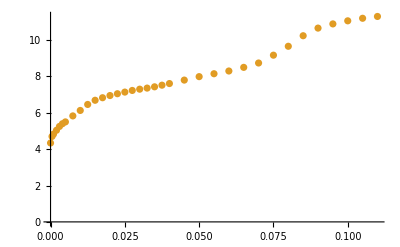

```mathematica
Vb16={0,1,2,4,6,8,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220}
pH16={4.34,4.7,4.83,5.04,5.25,5.4,5.5,5.83,6.13,6.46,6.69,6.83,6.95,7.05,7.14,7.23,7.3,7.36,7.43,7.52,7.61,7.8,7.99,8.15,8.3,8.5,8.74,9.17,9.66,10.24,10.66,10.89,11.06,11.2,11.3}
Thread[{Table[Vb[Hlist[[i]]],{i,Length[Hlist]}],pH}]
ListPlot[{Thread[{Table[Vb[Hlist[[i]]],{i,Length[Hlist]}],pH}],Thread[{Table[Vb16[[i]]/1000/2,{i,Length[Vb16]}],pH16}]},PlotRange->{Automatic,Automatic}]
```

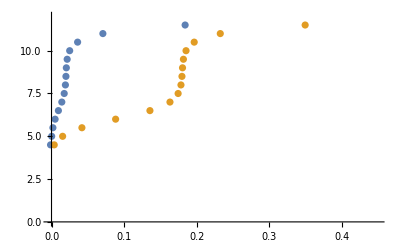

```mathematica
ListPlot[{Thread[{Table[Vb2[Hlist[[i]],0.1,10^(-3)],{i,Length[Hlist]}],pH}],Thread[{Table[Vb2[Hlist[[i]],.9,10^(-1)],{i,Length[Hlist]}],pH}]},PlotRange->{Automatic,Automatic}]
```

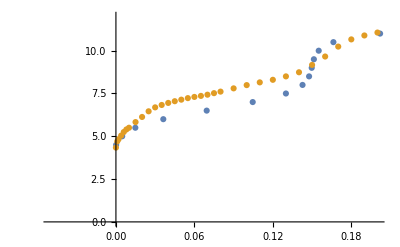

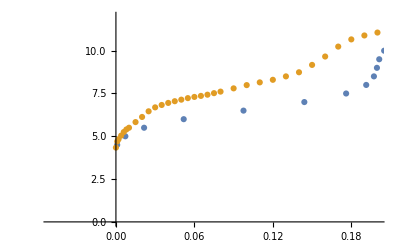

```mathematica
ListPlot[{Thread[{Table[Vb2[Hlist[[i]],0.75,0.9*10^(-3)],{i,Length[Hlist]}],pH}],Thread[{Table[Vb16[[i]]/1000,{i,Length[Vb16]}],pH16}]},PlotRange->{{-0.05,0.2},Automatic}]
ListPlot[{Thread[{Table[Vb3[Hlist[[i]],0.2,0.2*10^(-3)],{i,Length[Hlist]}],pH}],Thread[{Table[Vb16[[i]]/1000,{i,Length[Vb16]}],pH16}]},PlotRange->{{-0.05,0.2},Automatic}]
```

5

0.0032

0.1

1/10000000

10000

1/100000000000000

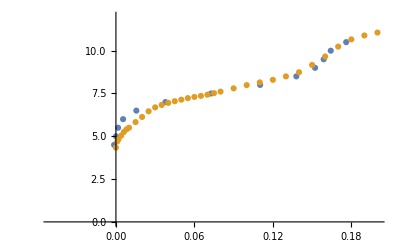

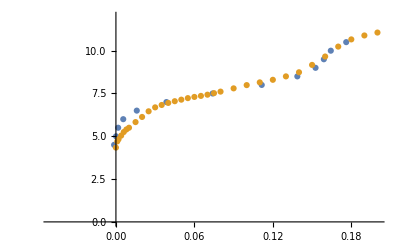

```mathematica
Va=5
Ainit=0.0032
Binit=0.1
Ka=10^(-7)
Ks=10^(4)
Kw=10^(-14)
Vb4[H_,f_,Ks_]:=((-2 H^5-2 H^4 (Binit+Ka)+√f H Ka √Ks √(Ainit^2 f Ka^2 Ks+Binit^2 f (H+Ka)^2 Ks+2 Ainit Binit (H+Ka) (2 H (Binit+H)+f Ka Ks-2 Kw))-H^2 (Binit+2 Ka) (f Ka Ks-2 Kw)-2 H^3 (Binit Ka+f Ka Ks-2 Kw)+2 Ka (f Ka Ks-Kw) Kw+H ((Ainit-Binit) f Ka^2 Ks+2 Ka (Binit+f Ks) Kw-2 Kw^2)) Va)/(2 (H+Ka) (H (Binit+H)-Kw) (H (Binit+H)+f Ka Ks-Kw))
ListPlot[{Thread[{Table[Vb4[Hlist[[i]],0.75,0.9*10^(-3)],{i,Length[Hlist]}],pH}],Thread[{Table[Vb16[[i]]/1000,{i,Length[Vb16]}],pH16}]},PlotRange->{{-0.05,0.2},Automatic}]
ListPlot[{Thread[{Table[Vb4[Hlist[[i]],0.3,3*10^(-3.1)],{i,Length[Hlist]}],pH}],Thread[{Table[Vb16[[i]]/1000,{i,Length[Vb16]}],pH16}]},PlotRange->{{-0.05,0.2},Automatic}]
```

```mathematica
Clear["`*"]
pH=List[4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12]
Hlist=Table[10^(-pH[[i]]),{i,Length[pH]}]
Vb16={0,1,2,4,6,8,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220}
pH16={4.34,4.7,4.83,5.04,5.25,5.4,5.5,5.83,6.13,6.46,6.69,6.83,6.95,7.05,7.14,7.23,7.3,7.36,7.43,7.52,7.61,7.8,7.99,8.15,8.3,8.5,8.74,9.17,9.66,10.24,10.66,10.89,11.06,11.2,11.3}
Va=5
Ainit=0.004
Binit=0.1
Ka=10^(-7.5)
Ks=10^(-2.5)
Kw=10^(-14)
n=.5
Vb5[H_,Ks_,Ka_,f_]:=((H Ka^2 Ks^2-f H Ka^2 Ks^2+H Ka Ks √(Binit^2 f^2 (H+Ka) ((-2+f)^2 H+f^2 Ka)+(-1+f)^2 Ka^2 Ks^2-2 Binit (-1+f) f^2 (H+Ka) (2 H^2+Ka Ks-2 Kw))-f^2 (H+Ka) (Binit H (2 H^2+Ka Ks-2 Kw)+2 (H^2-Kw) (H^2+Ka Ks-Kw))) Va)/(2 f^2 (H+Ka) (H (Binit+H)-Kw) (H (Binit+H)+Ka Ks-Kw))
VbHillKs[H_]:=((H^(3/2) Ka^n √Ks √(Ainit^2 H Ka^(2 n) Ks+Binit^2 H (H^n+Ka^n)^2 Ks+2 Ainit Binit (H^n+Ka^n) (H Ka^n Ks+2 H^n (H (Binit+H)-Kw)))-2 H^(2 n) (H^2-Kw) (H (Binit+H)-Kw)+H Ka^(2 n) Ks (Ainit H-H (Binit+2 H)+2 Kw)-H^n Ka^n (H^2 (2 H (H+Ks)+Binit (2 H+Ks))-2 H (Binit+2 H+Ks) Kw+2 Kw^2)) Va)/(2 (H^n+Ka^n) (H Ka^n Ks+H^n (H (Binit+H)-Kw)) (H (Binit+H)-Kw))
```

{4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12}

{0.0000316228,1/100000,3.16228×10^-6,1/1000000,3.16228×10^-7,1/10000000,3.16228×10^-8,1/100000000,3.16228×10^-9,1/1000000000,3.16228×10^-10,1/10000000000,3.16228×10^-11,1/100000000000,3.16228×10^-12,1/1000000000000}

{0,1,2,4,6,8,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220}

{4.34,4.7,4.83,5.04,5.25,5.4,5.5,5.83,6.13,6.46,6.69,6.83,6.95,7.05,7.14,7.23,7.3,7.36,7.43,7.52,7.61,7.8,7.99,8.15,8.3,8.5,8.74,9.17,9.66,10.24,10.66,10.89,11.06,11.2,11.3}

5

0.004

0.1

3.16228×10^-8

0.00316228

1/100000000000000

0.5

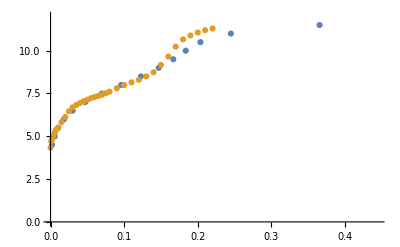

```mathematica
ListPlot[{Thread[{Table[VbHillKs[Hlist[[i]]],{i,Length[Hlist]}],pH}],Thread[{Table[Vb16[[i]]/1000,{i,Length[Vb16]}],pH16}]},PlotRange->{Automatic,Automatic}]
```

```mathematica
Clear["`*"]
```

```mathematica
Eliminate[{(H*A/HA)==Ka,
H*OH==Kw,
(HA*X)/(AX)==Ks,
CA==(1/q)*HA+(1/q)*A+AX,
H+B+HA==OH+X,
X==A+HA,
B==Vb*Binit/(Va+Vb),
CA==(Va*Ainit)/(Va+Vb)},{OH,HA,B,CA,AX,A,X}]
```

(H+Ka) Kw^2+Kw (-2 H^3-2 H^2 Ka-(H Ka Ks)/q-(Ka^2 Ks)/q-(2 Binit H^2 Vb)/(Va+Vb)-(2 Binit H Ka Vb)/(Va+Vb))==H (-H^4-H^3 Ka+Ainit Ka^2 Ks-(H^2 Ka Ks)/q-(H Ka^2 Ks)/q-(Binit^2 H^2 Vb^2)/(Va+Vb)^2-(Binit^2 H Ka Vb^2)/(Va+Vb)^2-(2 Binit H^3 Vb)/(Va+Vb)-(2 Binit H^2 Ka Vb)/(Va+Vb)-(Ainit Ka^2 Ks Vb)/(Va+Vb)-(Binit H Ka Ks Vb)/(q (Va+Vb))-(Binit Ka^2 Ks Vb)/(q (Va+Vb)))&&q≠0&&Va+Vb≠0

```mathematica
FullSimplify[Solve[%3,Vb]]
```

{{Vb→((-2 H (H^2-Kw)^2 q+Ka^2 Ks (-2 H^2+2 Kw+Ainit H q)-Binit H (H+Ka) (Ka Ks+2 (H^2-Kw) q)-2 Ka (H^2-Kw) (H Ks+H^2 q-Kw q)-H Ka √Ks √(Ainit^2 Ka^2 Ks q^2+2 Ainit Binit (H+Ka) q (Ka Ks+2 H^2 q-2 Kw q)+Binit^2 (H+Ka) ((H+Ka) Ks+4 Ainit H q^2))) Va)/(2 (H+Ka) (H (Binit+H)-Kw) (Ka Ks+H (Binit+H) q-Kw q))},{Vb→((-2 H (H^2-Kw)^2 q+Ka^2 Ks (-2 H^2+2 Kw+Ainit H q)-Binit H (H+Ka) (Ka Ks+2 (H^2-Kw) q)-2 Ka (H^2-Kw) (H Ks+H^2 q-Kw q)+H Ka √Ks √(Ainit^2 Ka^2 Ks q^2+2 Ainit Binit (H+Ka) q (Ka Ks+2 H^2 q-2 Kw q)+Binit^2 (H+Ka) ((H+Ka) Ks+4 Ainit H q^2))) Va)/(2 (H+Ka) (H (Binit+H)-Kw) (Ka Ks+H (Binit+H) q-Kw q))}}

```mathematica
pH=List[4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12]
Hlist=Table[10^(-pH[[i]]),{i,Length[pH]}]
Vb16={0,1,2,4,6,8,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220}
pH16={4.34,4.7,4.83,5.04,5.25,5.4,5.5,5.83,6.13,6.46,6.69,6.83,6.95,7.05,7.14,7.23,7.3,7.36,7.43,7.52,7.61,7.8,7.99,8.15,8.3,8.5,8.74,9.17,9.66,10.24,10.66,10.89,11.06,11.2,11.3}
Va=5
Ainit=0.004
Binit=0.1
Ka=10^(-5.05)
Ks=10^(-5.35)
Kw=10^(-14)
q=0.8
Vbq[H_]:=((-2 H (H^2-Kw)^2 q+Ka^2 Ks (-2 H^2+2 Kw+Ainit H q)-Binit H (H+Ka) (Ka Ks+2 (H^2-Kw) q)-2 Ka (H^2-Kw) (H Ks+H^2 q-Kw q)+H Ka √Ks √(Ainit^2 Ka^2 Ks q^2+2 Ainit Binit (H+Ka) q (Ka Ks+2 H^2 q-2 Kw q)+Binit^2 (H+Ka) ((H+Ka) Ks+4 Ainit H q^2))) Va)/(2 (H+Ka) (H (Binit+H)-Kw) (Ka Ks+H (Binit+H) q-Kw q))
```

{4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12}

{0.0000316228,1/100000,3.16228×10^-6,1/1000000,3.16228×10^-7,1/10000000,3.16228×10^-8,1/100000000,3.16228×10^-9,1/1000000000,3.16228×10^-10,1/10000000000,3.16228×10^-11,1/100000000000,3.16228×10^-12,1/1000000000000}

{0,1,2,4,6,8,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220}

{4.34,4.7,4.83,5.04,5.25,5.4,5.5,5.83,6.13,6.46,6.69,6.83,6.95,7.05,7.14,7.23,7.3,7.36,7.43,7.52,7.61,7.8,7.99,8.15,8.3,8.5,8.74,9.17,9.66,10.24,10.66,10.89,11.06,11.2,11.3}

5

0.004

0.1

8.91251×10^-6

4.46684×10^-6

1/100000000000000

0.8

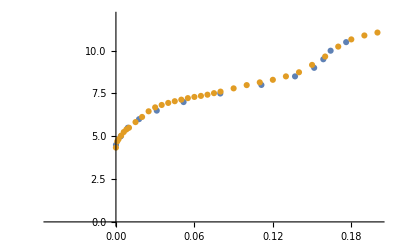

```mathematica
ListPlot[{Thread[{Table[Vbq[Hlist[[i]]],{i,Length[Hlist]}],pH}],Thread[{Table[Vb16[[i]]/1000,{i,Length[Vb16]}],pH16}]},PlotRange->{{-0.05,0.2},Automatic}]
```

### TRIPROTIC H*H2A/H3A==K1 expression for K1 H*HA/H2A==K2 expression for K2 H*A/HA==K3 expression for K3 H*OH==Kw water CA==H3A+H2A+HA+A mass balance for total concentration of acid H+B==H2A+2*HA+3*A+OH charge balance (B = the base cation) B==Vb Binit/(Va+Vb) concentration of base during titration CA==Va Ainit/(Va+Vb) concentration of acid during titration

```mathematica
Eliminate[{HA*H2A/H3A==K1,
H*HA/H2A==K2,
H*A/HA==K3,
H*OH==Kw,
CA==H3A+H2A+HA+A,
H+B==H2A+2*HA+3*A+OH,
B==Vb*Binit/(Va+Vb),
CA==Va*Ainit/(Va+Vb)},{OH,HA,H2A,B,CA,H3A,A}]
```

H^2 K2 Kw^2+Kw (-H^4 K1-2 H^4 K2-3 H^3 K1 K2-2 H^2 K1 K2^2-4 H^2 K1 K2 K3-5 H K1 K2^2 K3-3 K1 K2^2 K3^2-(2 Binit H^3 K2 Vb)/(Va+Vb))==H (Ainit H^4 K1-H^5 K1-H^5 K2+4 Ainit H^3 K1 K2-3 H^4 K1 K2+4 Ainit H^2 K1 K2^2-2 H^3 K1 K2^2+6 Ainit H^2 K1 K2 K3-4 H^3 K1 K2 K3+12 Ainit H K1 K2^2 K3-5 H^2 K1 K2^2 K3+9 Ainit K1 K2^2 K3^2-3 H K1 K2^2 K3^2-(Binit^2 H^3 K2 Vb^2)/(Va+Vb)^2-(Ainit H^4 K1 Vb)/(Va+Vb)-(Binit H^4 K1 Vb)/(Va+Vb)-(2 Binit H^4 K2 Vb)/(Va+Vb)-(4 Ainit H^3 K1 K2 Vb)/(Va+Vb)-(3 Binit H^3 K1 K2 Vb)/(Va+Vb)-(4 Ainit H^2 K1 K2^2 Vb)/(Va+Vb)-(2 Binit H^2 K1 K2^2 Vb)/(Va+Vb)-(6 Ainit H^2 K1 K2 K3 Vb)/(Va+Vb)-(4 Binit H^2 K1 K2 K3 Vb)/(Va+Vb)-(12 Ainit H K1 K2^2 K3 Vb)/(Va+Vb)-(5 Binit H K1 K2^2 K3 Vb)/(Va+Vb)-(9 Ainit K1 K2^2 K3^2 Vb)/(Va+Vb)-(3 Binit K1 K2^2 K3^2 Vb)/(Va+Vb))&&Va+Vb≠0

```mathematica
Simplify[Solve[%14,{Vb}]]
```

{{Vb→-(((Binit H^5 K1+2 H^6 K1+2 Binit H^5 K2+2 H^6 K2+3 Binit H^4 K1 K2+6 H^5 K1 K2+2 Binit H^3 K1 K2^2+4 H^4 K1 K2^2+4 Binit H^3 K1 K2 K3+8 H^4 K1 K2 K3+5 Binit H^2 K1 K2^2 K3+10 H^3 K1 K2^2 K3+3 Binit H K1 K2^2 K3^2+6 H^2 K1 K2^2 K3^2-Ainit H K1 (H^2+2 H K2+3 K2 K3)^2+H^3 √K1 √(Binit^2 K1 (H^2+H K2+K2 K3)^2+Ainit^2 K1 (H^2+2 H K2+3 K2 K3)^2+2 Ainit Binit (H^3 (2 Binit+3 K1) K2+H^4 (K1+2 K2)+5 H K1 K2^2 K3+3 K1 K2^2 K3^2+2 H^2 K2 (K1 K2+2 K1 K3-Kw)))+2 H^2 √K1 K2 √(Binit^2 K1 (H^2+H K2+K2 K3)^2+Ainit^2 K1 (H^2+2 H K2+3 K2 K3)^2+2 Ainit Binit (H^3 (2 Binit+3 K1) K2+H^4 (K1+2 K2)+5 H K1 K2^2 K3+3 K1 K2^2 K3^2+2 H^2 K2 (K1 K2+2 K1 K3-Kw)))+3 H √K1 K2 K3 √(Binit^2 K1 (H^2+H K2+K2 K3)^2+Ainit^2 K1 (H^2+2 H K2+3 K2 K3)^2+2 Ainit Binit (H^3 (2 Binit+3 K1) K2+H^4 (K1+2 K2)+5 H K1 K2^2 K3+3 K1 K2^2 K3^2+2 H^2 K2 (K1 K2+2 K1 K3-Kw)))-2 H^4 K1 Kw-2 Binit H^3 K2 Kw-4 H^4 K2 Kw-6 H^3 K1 K2 Kw-4 H^2 K1 K2^2 Kw-8 H^2 K1 K2 K3 Kw-10 H K1 K2^2 K3 Kw-6 K1 K2^2 K3^2 Kw+2 H^2 K2 Kw^2) Va)/(2 (H^3 (Binit+3 K1) K2+H^4 (K1+K2)+5 H K1 K2^2 K3+3 K1 K2^2 K3^2+H^2 K2 (2 K1 (K2+2 K3)-Kw)) (Binit H+H^2-Kw)))},{Vb→((-Binit H^5 K1-2 H^6 K1-2 Binit H^5 K2-2 H^6 K2-3 Binit H^4 K1 K2-6 H^5 K1 K2-2 Binit H^3 K1 K2^2-4 H^4 K1 K2^2-4 Binit H^3 K1 K2 K3-8 H^4 K1 K2 K3-5 Binit H^2 K1 K2^2 K3-10 H^3 K1 K2^2 K3-3 Binit H K1 K2^2 K3^2-6 H^2 K1 K2^2 K3^2+Ainit H K1 (H^2+2 H K2+3 K2 K3)^2+H^3 √K1 √(Binit^2 K1 (H^2+H K2+K2 K3)^2+Ainit^2 K1 (H^2+2 H K2+3 K2 K3)^2+2 Ainit Binit (H^3 (2 Binit+3 K1) K2+H^4 (K1+2 K2)+5 H K1 K2^2 K3+3 K1 K2^2 K3^2+2 H^2 K2 (K1 K2+2 K1 K3-Kw)))+2 H^2 √K1 K2 √(Binit^2 K1 (H^2+H K2+K2 K3)^2+Ainit^2 K1 (H^2+2 H K2+3 K2 K3)^2+2 Ainit Binit (H^3 (2 Binit+3 K1) K2+H^4 (K1+2 K2)+5 H K1 K2^2 K3+3 K1 K2^2 K3^2+2 H^2 K2 (K1 K2+2 K1 K3-Kw)))+3 H √K1 K2 K3 √(Binit^2 K1 (H^2+H K2+K2 K3)^2+Ainit^2 K1 (H^2+2 H K2+3 K2 K3)^2+2 Ainit Binit (H^3 (2 Binit+3 K1) K2+H^4 (K1+2 K2)+5 H K1 K2^2 K3+3 K1 K2^2 K3^2+2 H^2 K2 (K1 K2+2 K1 K3-Kw)))+2 H^4 K1 Kw+2 Binit H^3 K2 Kw+4 H^4 K2 Kw+6 H^3 K1 K2 Kw+4 H^2 K1 K2^2 Kw+8 H^2 K1 K2 K3 Kw+10 H K1 K2^2 K3 Kw+6 K1 K2^2 K3^2 Kw-2 H^2 K2 Kw^2) Va)/(2 (H^3 (Binit+3 K1) K2+H^4 (K1+K2)+5 H K1 K2^2 K3+3 K1 K2^2 K3^2+H^2 K2 (2 K1 (K2+2 K3)-Kw)) (Binit H+H^2-Kw))}}

```mathematica
Clear[" *"]
Solve[Vb*10^(-pH)==(γ1/γ2)*Ka*(Ve–Vb),Vb]
```

{{Vb→0}}

```mathematica
γ1=1
γ2=1
```

```mathematica
pH=List[4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12]
Vblist=List[0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150]
```

{4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12}

{0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150}

```mathematica
lhs[pH_,Vb_]:=Vb*10^(-pH)
rhs[Vb_,Ka_,γ1_,γ2_,Ve_]:=(γ1/γ2)*Ka*(Ve-Vb)
```

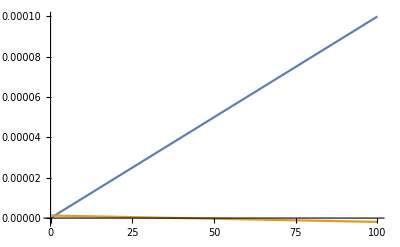

```mathematica
Plot[{lhs[6,x],rhs[x,10^(-7.5),1,1,40]},{x,0,100}]
```

```mathematica
Vb16={0,1,2,4,6,8,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220}
pH16={4.34,4.7,4.83,5.04,5.25,5.4,5.5,5.83,6.13,6.46,6.69,6.83,6.95,7.05,7.14,7.23,7.3,7.36,7.43,7.52,7.61,7.8,7.99,8.15,8.3,8.5,8.74,9.17,9.66,10.24,10.66,10.89,11.06,11.2,11.3}
```

{0,1,2,4,6,8,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220}

{4.34,4.7,4.83,5.04,5.25,5.4,5.5,5.83,6.13,6.46,6.69,6.83,6.95,7.05,7.14,7.23,7.3,7.36,7.43,7.52,7.61,7.8,7.99,8.15,8.3,8.5,8.74,9.17,9.66,10.24,10.66,10.89,11.06,11.2,11.3}

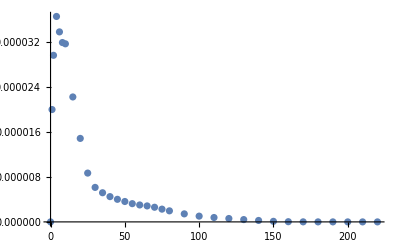

```mathematica
ListPlot[Thread[{Evaluate[Vb16,lhs[pH16,Vb16]]}],PlotRange->{Automatic,Automatic}]
```

```mathematica
Vb16
```

{0,1,2,4,6,8,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220}

{{0.,0},{0.0000199526,1},{0.0000295822,2},{0.0000364804,4},{0.0000337405,6},{0.0000318486,8},{0.0000316228,10},{0.0000221866,15},{0.0000148262,20},{8.66842×10^-6,25},{6.12521×10^-6,30},{5.17688×10^-6,35},{4.48807×10^-6,40},{4.01063×10^-6,45},{3.62218×10^-6,50},{3.23864×10^-6,55},{3.00712×10^-6,60},{2.83735×10^-6,65},{2.60075×10^-6,70},{2.26496×10^-6,75},{1.96377×10^-6,80},{1.4264×10^-6,90},{1.02329×10^-6,100},{7.7874×10^-7,110},{6.01425×10^-7,120},{4.11096×10^-7,130},{2.54758×10^-7,140},{1.01412×10^-7,150},{3.50042×10^-8,160},{9.78248×10^-9,170},{3.93797×10^-9,180},{2.44767×10^-9,190},{1.74193×10^-9,200},{1.32501×10^-9,210},{1.10261×10^-9,220}}

```mathematica
NSolve[f^2-1.3*f+1.3==0,f]
```

{{f→0.65-0.93675 ⅈ},{f→0.65+0.93675 ⅈ}}